```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<Segment.wl
```

```mathematica
<<Ocr.wl
```

```mathematica
ocrChinese@imageScaled[-Graphics-,5]
```

长久以来, 机器视觉认知一直是人们研究的热点, 它是研究使用机器或计算

```mathematica
plot:=ArrayPlot[#,ColorRules->{0->Blue,1->White,2->Red,3->Green},Mesh->All]&(*全黑会画成全白，坑了。用蓝代替黑*)
```

```mathematica
i=Import@"data/simple01.bmp"
```

-Graphics-

```mathematica
(*zhLines=i//segment//(#//splitByGreen//turnBlack/@#&//mergeSplitBy//Image[#,"Bit",Magnification->1]&//ColorNegate)&/@#&;*)
```

```mathematica
(*宽高比*)
ratioWidthHight[mts_]:=mts//Dimensions/@#&//(#[[1]]/#[[2]]&)/@#&
```

```mathematica
zhLines=i//imageLines;
```

```mathematica
zhLines//TableForm
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

```mathematica
zhLines//imageScaled[#,5]&/@#&//ocrChinese/@#&//TableForm
```

```mathematica
greenReds=zhLines//labelGreenRed/@#&;
```

```mathematica
greenRed=zhLines//First//labelGreenRed;
```

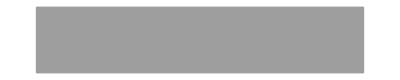

```mathematica
greenRed//plot
```

```mathematica
characters=greenRed//splitByGreenClean;
```

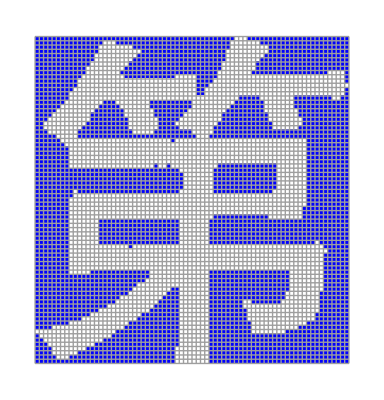
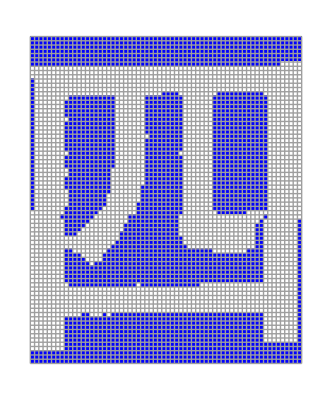
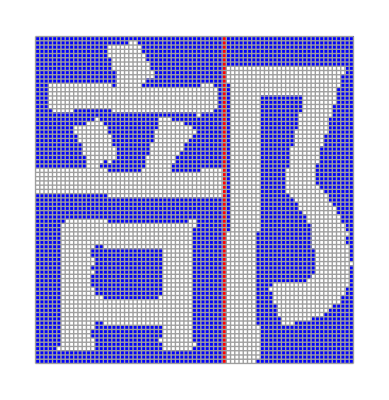
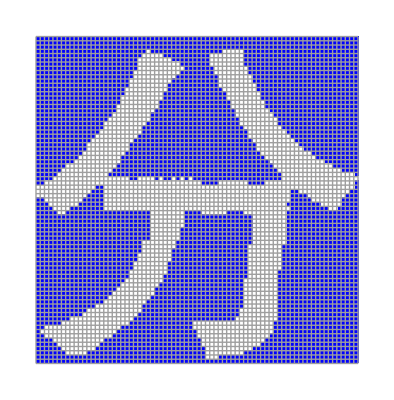
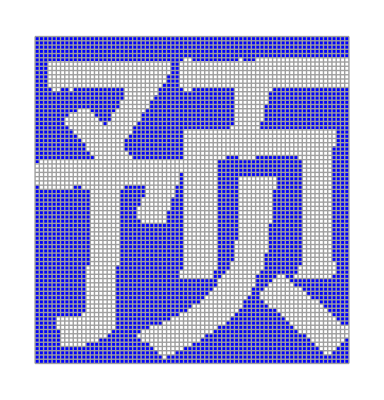
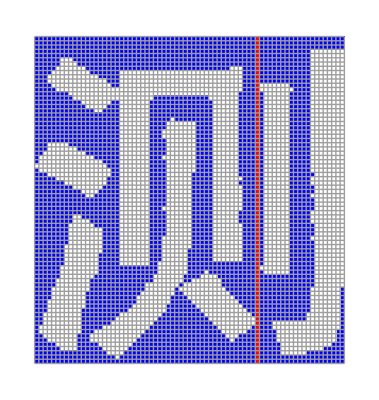
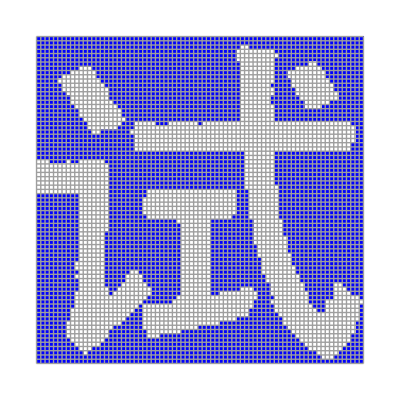
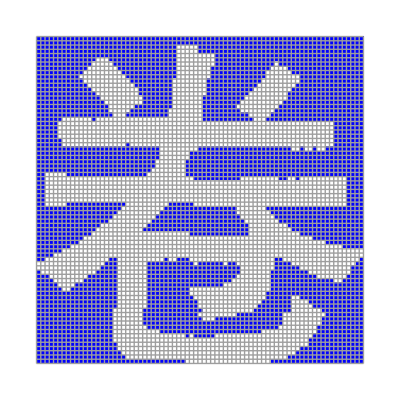

```mathematica
characters//plot/@#&
```

```mathematica
characterss=greenReds//splitByGreenClean/@#&;
```

```mathematica
characters=characterss//Flatten[#,1]&;
```

```mathematica
ratio=characters//ratioWidthHight//FindClusters//Sort[#, Length[#1]>Length[#2]&]&//First
```

{77/74,77/64,77/75,77/76,77/74,77/73,1,1,59/58,59/60,59/58,59/58,59/60,43/37,43/39,43/40,43/40,43/40,43/40,43/41,43/41,43/40,43/41,43/41,43/40,43/40,43/36,43/40,43/40,43/39,43/34,43/36,43/39,43/41,43/40,43/41,43/41,43/85,43/40,43/39,43/42,43/39,43/40,43/41,43/41,43/39,43/37,43/41,43/40,43/41,43/40,43/37,43/41,20/17,1,1,40/41,1,40/41,40/41,40/41,40/41,40/39,10/9,1,40/39,42/41,21/20,42/41,14/13,21/20,14/13,42/31,21/20,21/20,7/6,14/13,14/13,14/13,21/19,21/20,21/20,21/20,42/41,21/20,42/37,21/20,14/13,21/41,42/37,21/20,14/13,1,1,41/40,41/38,41/40,41/40,41/40,41/39,41/39,41/39,41/40,41/40,1,41/36,41/39,41/40,41/34,41/40,41/40,1,41/39,1,41/40,1,41/40,41/38,41/40,41/38,43/41,43/41,43/41,43/41,43/39,43/41,43/41,43/41,43/40,43/41,43/40,43/82,43/34,43/40,43/41,43/38,43/38,43/39,43/40,43/40,43/38,43/42,43/39,43/36,43/41,43/41,43/40,43/39,43/41,43/41,43/39,43/40,43/36,43/34,43/40,43/35,43/39,43/39,43/41,43/40,43/37,43/84,43/35,43/40,43/42,43/37,43/41,43/40,43/40,43/39,43/36,43/39,43/40,43/40,43/41,43/40,43/34,43/41,43/40,43/41,43/41,43/36,43/40,43/39,6/5,21/20,21/20,14/13,6/5,42/41,21/20,42/85,1,41/39,41/40,41/40,41/38,41/84,41/35,14/13,21/19,21/19,21/20,42/41,42/41,21/20,42/41,7/6,21/20,22/21,11/21,11/9,11/10,44/41,22/19,11/10,11/10,11/10,44/41,11/10,44/39,44/41,44/39,11/10,11/10,22/19,22/21,44/41,11/10,14/13,14/13,14/13,1,14/13,21/20,21/20,21/20,1,7/6,21/20,14/13,14/13,21/20,6/5,21/20,6/5,21/20,42/41,21/20,21/20,21/20,21/20,41/40,1,1,41/40,1,41/40,1,41/40,11/10,11/10,11/10,44/83,11/10,11/10,44/39,22/21,11/10,11/10,44/41,11/9,44/41,11/10,11/10,11/10,44/39,44/41,44/39,11/10,44/41,44/39,11/9,44/41,11/10,22/19,11/10,44/39,22/17,11/10,44/41,11/10,22/19,21/20,21/20,42/41,21/20,1,21/17,14/13,21/20,21/20,21/20,21/20,21/17,21/20,14/13,21/20,14/13,14/13,42/41,40/41,1,1,20/17,1,40/39,1,44/39,44/41,44/39,11/10,11/10,44/41,11/10,11/9,44/39,44/41,44/39,11/10,11/10,11/10,44/41,44/37,11/9,11/10,44/39,44/39,11/10,11/10,44/41,44/41,11/10,43/34,43/41,43/41,43/39,43/40,43/38,43/39,43/39,43/39,43/40,43/41,43/40,43/39,43/40,43/40,43/40,43/39,43/40,43/38,43/38,43/40,43/40,43/40,6/5,42/41,14/13,21/20,21/19,7/6,14/13,14/13,14/13,21/20,21/20,14/13,21/20,6/5,14/13,14/13,21/20,21/19,21/19,21/20,14/13,42/41,44/41,11/10,44/39,22/21,44/39,11/10,11/10,11/9,44/41,11/10,44/39,11/10,44/39,44/39,44/41,11/10,11/10,11/10,44/41,11/10,44/37,44/39,44/41,44/39,44/41,22/21,44/39,11/9,44/39,11/9,44/39,44/39,41/83,1,41/40,41/40,41/40,1,41/37,1,41/39,41/40,41/40,41/40,41/39,1,21/17,21/19,21/20,7/6,14/13,42/41,21/20,42/41,21/20,21/20,21/20,42/41,42/41,7/6,40/41,1,40/39,40/33,8/17,40/41,10/9,44/41,44/41,11/10,44/41,44/39,11/10,11/10,11/9,44/41,11/10,44/39,11/10,11/10,44/39,44/41,44/41,11/9,44/41,11/9,11/10,44/41,44/41,22/19,44/35,11/10,11/10,22/21,11/10,11/10,11/10,11/10,7/6,14/13,42/41,21/20,21/20,21/20,42/41,1/2,14/13,21/20,42/41,14/13,21/19,14/13,42/41,42/37,42/41,14/13,21/20,14/11,21/20,42/41,14/13,21/20,21/20,42/41,21/20,42/41,14/13,21/20,21/20,42/41}

```mathematica
characters//ratioWidthHight
```

{77/74,77/64,77/75,77/76,77/74,77/73,1,1}

```mathematica
Quit[]
```